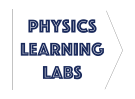
# -Graphics- Mathematica Formatting

## Notebook Styling

Primarily uses default styling, with a few additions.

Styles used are: Title, Section, Subsection, Subsubsection, Item, Text, Input

Here is the title cell with PLL figure.

To generate gray horizontal line above and below sections, subsections, etc, use

```mathematica
CellPrint[Cell["Background", "Title",
 CellFrame->{{0, 0}, {1, 1}},
 CellFrameColor->GrayLevel[.7]]]
```

```mathematica
CellPrint[Cell["Experiment", "Section",
 CellFrame->{{0, 0}, {1, 1}},
 CellFrameColor->GrayLevel[.7]]]
```

```mathematica
CellPrint[Cell["Data Collection", "Subsection",
 CellFrame->{{0, 0}, {1, 1}},
 CellFrameColor->GrayLevel[.7]]]
```

```mathematica
CellPrint[Cell["Background", "Subsubsection",
 CellFrame->{{0, 0}, {1, 1}},
 CellFrameColor->GrayLevel[.7]]]
```

#### Background

Use CellTags for questions (Q1, Q2, ..) equations (Eq.(1),..) and figures (Fig.(1), ..). Cell->Cell Tags

Inline cell tag reference italicized (Q1, Eq.(1), ..)

Light orange background for code input, light yellow for text input (Format->Background Color)

Red cell dingbat for action item. (Style->Item)

Requires an action

Here is a reference for the submission disclaimer

```mathematica
CellPrint[Cell["Background", "Title",
 CellFrame->{{0, 0}, {0, 10}},
 CellFrameColor->GrayLevel[.7]]]
```

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).

All figures are framed. Cell figures are assigned ordered cell tags (Fig.(3), etc..). To frame a figure or equation, Insert > Typesetting > Add Frame

## Cell Properties

Select desired cells, go to Format > Options Inspector > Cell Options > General Properties. Here you may check or uncheck the Deletable or Editable options to toggle edit-ability/delete-ability.

For student version notebooks, all cells are default set to uneditable and undeleteable other than question input or code input cells.

## Lab 3

Used to generate blank plot

```mathematica
ListPlot[{{-2,-1}},AxesLabel->{"μ_k","g (m/s^2)"},PlotRange->{{-0.001,0.02},{8.6,11}},GridLines->Automatic,AxesOrigin->{-0.001,8.6}]
```

## Lab 6

Used to generate trials array

```mathematica
Text[Grid[{{"Trial 1 (Vertical Disc)", "Trial 2 (Disc)", "Trial 3 (Disc+Ring)"},
{-Graphics-,-Graphics-,-Graphics-},
{"Trial 4 (Platform)", "Trial 5 (Platform-Square-0cm)", "Trial 6 (Platform-Square-5cm)"},
{-Graphics-,-Graphics-,-Graphics-}},
Frame->All]]
```

Trial 1 (Vertical Disc) | Trial 2 (Disc) | Trial 3 (Disc+Ring)
-Graphics- | -Graphics- | -Graphics-
Trial 4 (Platform) | Trial 5 (Platform-Square-0cm) | Trial 6 (Platform-Square-5cm)
-Graphics- | -Graphics- | -Graphics-

## Lab 8

Used to generate trials array

```mathematica
Text[Grid[{
{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{"θ_Eq=0°", "θ_S≈(5-10)°", "θ_M=90°","θ_L≈(178-180)°"}},Frame->All]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
θ_Eq=0° | θ_S≈(5-10)° | θ_M=90° | θ_L≈(178-180)°

Used to generate data table

```mathematica
Text[Grid[{
{" ","θ_0","ω","T","2π/T"},{"θ_S","0"," "," "},{"θ_M"," "," "," "},{"θ_L"," "," "," "}},Frame->All]]
```

| θ_0 | ω | T | 2π/T
θ_S | 0 |   |   | 
θ_M |   |   |   | 
θ_L |   |   |   |

| θ_0 | ω | T | 2π/T
θ_S |   |   |   | 
θ_M |   |   |   | 
θ_L |   |   |   |

## Lab 9

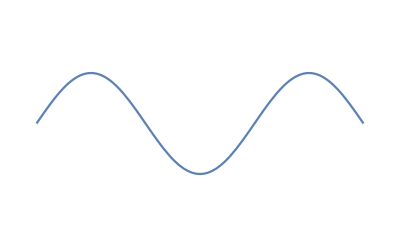

```mathematica
Plot[Sin[x],{x,0,3π},Axes->False,PlotRange->{{0,3π},{-2,2}}]
```

## Prelab 10

Generate standing wave images

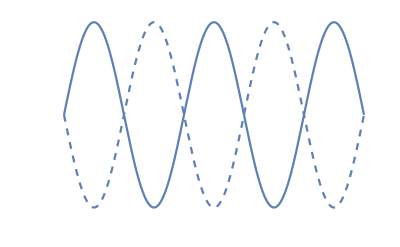

```mathematica
Plot[{Sin[1t],-Sin[1t]},{t,0,5π},AxesLabel->{"t (s)", "y (m)"},PlotStyle->{Automatic,{Dashed ,ColorData[97,"ColorList"][[1]]}},Axes->False]
```